SimulationTools > Black Holes

# Black Holes

A simulation can contain any number of black holes, numbered 1, 2, 3, ... .  Functions are provided to get the mass and spin of each black hole.

## Working with black holes

ReadBlackHoleMass | ReadBlackHoleSpin
ReadBlackHoleIrreducibleMass |

Functions for reading black hole information.

### Mass

The function ReadBlackHoleMass gives the mass of one of the black holes as a function of time.  This is the physical mass of the black hole, including the spin contribution.

```mathematica
mass1=ReadBlackHoleMass[$SimulationToolsTestSimulation,1]
```

DataTable[<151>,{{0.,300.}}]

```mathematica
ToList[mass1]//Short
```

{{0.,0.500004},«149»,{300.,0.952048}}

When simulating binary systems, the inspiralling black holes are conventionally taken to be 1 and 2, and the final merged black hole is 3.

```mathematica
mass2=ReadBlackHoleMass[$SimulationToolsTestSimulation,2]
```

DataTable[<151>,{{0.,300.}}]

```mathematica
mass3=ReadBlackHoleMass[$SimulationToolsTestSimulation,3]
```

DataTable[<97>,{{108.,300.}}]

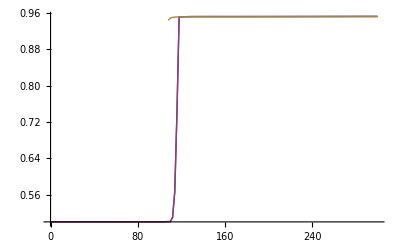

```mathematica
ListLinePlot[{mass1,mass2,mass3}]
```

### Spin

The function ReadBlackHoleSpin gives the spin of one of the black holes as a function of time.  This is the dimensionful angular momentum; i.e. it has units of [mass]^2.

```mathematica
spin1={spin1x,spin1y,spin1z}=ReadBlackHoleSpin[$SimulationToolsTestSimulation,1]
```

{DataTable[<151>,{{0,300}}],DataTable[<151>,{{0,300}}],DataTable[<151>,{{0,300}}]}

```mathematica
spin2={spin2x,spin2y,spin2z}=ReadBlackHoleSpin[$SimulationToolsTestSimulation,1]
```

{DataTable[<151>,{{0,300}}],DataTable[<151>,{{0,300}}],DataTable[<151>,{{0,300}}]}

```mathematica
spin3={spin3x,spin3y,spin3z}=ReadBlackHoleSpin[$SimulationToolsTestSimulation,3]
```

{DataTable[<151>,{{0,300}}],DataTable[<151>,{{0,300}}],DataTable[<151>,{{0,300}}]}

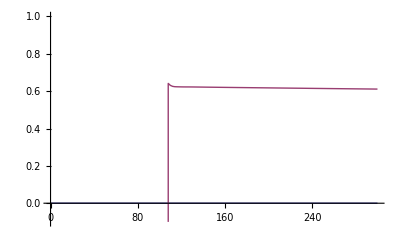

```mathematica
ListLinePlot[{spin1x,spin3z},PlotRange->{-0.1,1}]
```

Since the result is a list, you can compute the magnitude of the spin vector using the Norm function:

```mathematica
spin1Norm=Norm[spin1]
```

DataTable[<151>,{{0,300}}]

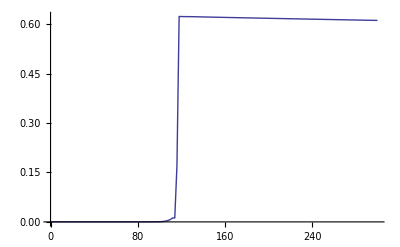

```mathematica
ListLinePlot[spin1Norm]
```

You can also compute the dimensionless spin by dividing by the mass squared:

```mathematica
j1=spin1Norm/mass1^2//WithResampling
```

DataTable[<151>,{{0,300}}]

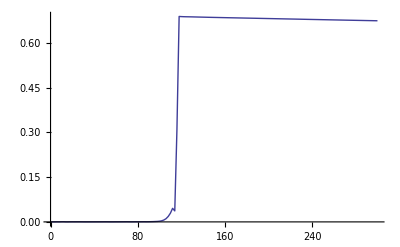

```mathematica
ListLinePlot[j1]
```

### Irreducible mass

If there is no spin information available in the simulation then ReadBlackHoleMass cannot be used.  If it is known that the spins are negligible, then the irreducible mass can be used as a mass measurement.

```mathematica
massIrr1=ReadBlackHoleIrreducibleMass[$SimulationToolsTestSimulation,1]
```

DataTable[<150>,{{0.,300.}}]

## Implementation notes

SimulationTools obtains black hole information from any of the following sources:

AHFinderDirect and QuasiLocalMeasures Cactus output;

Numerical Relativity Data Format (NRDF) output files

In both cases, the black holes are numbered according to the output data. So black hole 1 corresponds to AHFinderDirect horizon 1 (QuasiLocalMeasures horizon 0), or NRDF body 1 from the metadata file.

DataTable

NumericalRelativity